```mathematica
encodeID[expr_]:=StringReplace[Developer`EncodeBase64@BinarySerialize@expr,"/"->"~"]
decodeID[expr_]:=BinaryDeserialize@Developer`DecodeBase64ToByteArray@StringReplace[expr,"~"->"/"]
```

```mathematica
ClearAll[getFileNames,fromFileNameGetGeoRange]

getFileNames[folderName_] := 
	FileNames["*.png",FileNameJoin[{NotebookDirectory[],folderName}],Infinity];

fromFileNameGetGeoRange[fileName_] := 
	decodeID[FileBaseName@fileName]["GeoRange"];
```

```mathematica
ClearAll[associateFilesToGeoRange]
associateFilesToGeoRange[fileNames_] := 
	Map[
		File[#] -> fromFileNameGetGeoRange[#] &,
		getFileNames[fileNames]
	]
```

```mathematica
calculateError[net_,data_] :=(Abs[net[data[[All,1]]]-data[[All,2]]])/data[[All,2]]//Mean
calculateMeanSq[net_,data_] :=(Abs[net[data[[All,1]]]-data[[All,2]]])^2//Mean
```

```mathematica
ClearAll[sortPerformance]
sortPerformance[net_,data_] := 
	With[
		{img = Map[Import,data[[All,1]]], correspondingScale = data[[All,2]]},
		SortBy[
			AssociationThread[img,Transpose[{net[img],correspondingScale}]],
			Abs[First[#] - Last[#]]&
		]
	]
```

```mathematica
ClearAll[testing,validation,testing]

training2 = RandomSample@associateFilesToGeoRange["training"];
validation2 = RandomSample@associateFilesToGeoRange["validation"];
testing2 = RandomSample@associateFilesToGeoRange["testing"];

(*TableForm[
	{{"Training","Validation","Testing"},
	{Length@training,Length@validation,Length@testing}}
]

TableForm[
	{{"Training Data distribution","Validation Data distribution","Testing Data distribution"},
	{Histogram[Sort@training[[All,2]],PlotRange->All],Histogram[Sort@validation[[All,2]],PlotRange->All],Histogram[Sort@testing[[All,2]],PlotRange->All]}}
]*)
```

```mathematica
Min[testing[[All,2]]]
```

0.0666667

```mathematica
ClearAll[tnet]
tnet = Import["/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/wolframScriptCodes/moreImagesToTrain/amazonTrainedNet.wlnet"]
(*tnet = Import["/Users/mehmetsahin/Desktop/wolframscpt/more/moreImagesToTrain/progress/2018-07-09T20:54:19_0_30_12270_1.04e-2_4.34e-2.wlnet"]*)
```

Import::nffil: File not found during Import.

$Failed

```mathematica
ClearAll[dataset2]
dataset2 = sortPerformance[tnet,testing];
dataset2[[1;;4]]  (*Best 3*)
dataset2[[-4;;]] (*Worst 3*)
```

<|-Graphics-→{1.14055,1.13986},-Graphics-→{1.28119,1.28017},-Graphics-→{1.04051,1.04159},-Graphics-→{0.6932,0.694391}|>

<|-Graphics-→{0.468719,1.30694},-Graphics-→{2.20637,3.05436},-Graphics-→{2.80508,3.84052},-Graphics-→{3.13268,1.83812}|>

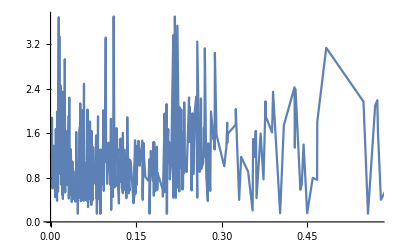

```mathematica
ListLinePlot[Transpose[{Map[Abs[First[#]-Last[#]]&,Values[dataset2]],Map[First[#]&,Values[dataset2]]}]]
```

```mathematica
calculateError[tnet,testing]
```

0.205119